# Randvärdesproblem

## Exempel från föreläsningen

### Exempel 1

{2 y[1]+4. (-y[0]+y[1])==1,2 y[2]+4. (-y[1]+y[2])==1,2 y[3]+4. (-y[2]+y[3])==1,2 y[4]+4. (-y[3]+y[4])==1}

{y[1]→0.166667,y[2]→0.277778,y[3]→0.351852,y[4]→0.401235}

{{0,0},{1/4,0.166667},{1/2,0.277778},{3/4,0.351852},{1,0.401235}}

1/2 ⅇ^(-2 x) (-1+ⅇ^(2 x))

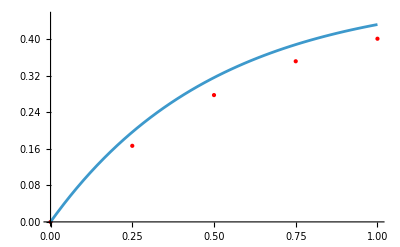

```mathematica
Remove["Global`*"]
ode=y'[x]+2y[x]==1;
{a,b,ya,ymax}={0,1.,0,0.45};
n=4;
h=(b-a)/n;
dy=(y[i]-y[i-1])/h;
ekv=Table[ode/.{x->a+i*h,y'[x]->dy,y[x]->y[i]},{i,1,n}]
sol=Solve[ekv/.y[0]->ya][[1]]
yFdm=Table[{i/n,y[i]},{i,0,n}]/.sol/.y[0]->ya
lp=ListPlot[yFdm,PlotStyle->{Red,PointSize[Medium]},PlotRange->{0,ymax}];
yM=y[x]/.DSolve[{ode,y[a]==ya},y[x],x][[1]]
pl=Plot[yM,{x,a,b},PlotRange->{0,ymax}];
Show[lp,pl]
```

### Exempel 2

{y[1]+7.5 (-y[0]+y[2])+25. (y[0]-2 y[1]+y[2])==0.008,y[2]+7.5 (-y[1]+y[3])+25. (y[1]-2 y[2]+y[3])==0.064,y[3]+7.5 (-y[2]+y[4])+25. (y[2]-2 y[3]+y[4])==0.216,y[4]+7.5 (-y[3]+y[5])+25. (y[3]-2 y[4]+y[5])==0.512}

{y[1]→1.10378,y[2]→1.66441,y[3]→1.91705,y[4]→2.00074}

{{0,0},{1/5,1.10378},{2/5,1.66441},{3/5,1.91705},{4/5,2.00074},{1,2.}}

-3.28542 (38.3513+1. ⅇ^((-3/2-(√5)/2) x)-39.3513 ⅇ^((-3/2+(√5)/2) x)-14.61 x+2.73938 x^2-0.304375 x^3)

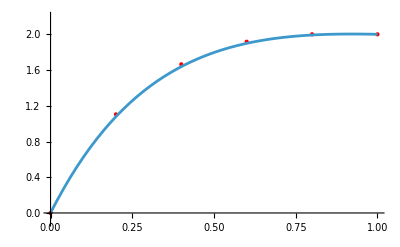

```mathematica
Remove["Global`*"]
ode=y''[x]+3y'[x]+y[x]==x^3;
{a,b,ya,yb}={0.,1.,0,2.};
n=5;
h=(b-a)/n;
dy=(y[i+1]-y[i-1])/(2h);
d2y=(y[i+1]-2*y[i]+y[i-1])/h^2;
ekv=Table[ode/.{x->a+i*h,y''[x]->d2y,y'[x]->dy,y[x]->y[i]},{i,1,n-1}]
sol=Solve[ekv/.{y[0]->ya,y[n]->yb}][[1]]
yFdm=Table[{i/n,y[i]},{i,0,n}]/.sol/.{y[0]->ya,y[n]->yb}
lp=ListPlot[yFdm,PlotStyle->{Red,PointSize[Medium]},PlotRange->{-0.1,2.2}];
yM=y[x]/.DSolve[{ode,y[a]==ya,y[b]==yb},y[x],x][[1]]
pl=Plot[yM,{x,a,b},PlotRange->{-0.1,2.2}];
Show[lp,pl]
```

### Exempel 3

```mathematica
Remove["Global`*"]
ode=alfa *y''[x]+beta*y'[x]+gamma*y[x]==g[x];
g[x_]=x^3;
{alfa,beta,gamma}={1,3,1};
{a,b,ya,yb}={0.,1.,0,2.};
n=5;
h=(b-a)/n;
al=alfa-beta*h/2;
ac=-2*alfa+gamma*h^2;
ar=alfa+beta*h/2;
A=SparseArray[{
Band[{1,1}]->ConstantArray[ac,n-1],
Band[{2,1}]->ConstantArray[al,n-2],
Band[{1,2}]->ConstantArray[ar,n-2]},{n-1,n-1}
];
xInre=Table[a+i*h,{i,1,n-1}];
Blast=h^2*g[xInre];
Brand=ConstantArray[0,n-1]; 
Brand[[1]]=-al*ya; 
Brand[[n-1]]=-ar*yb;
B=Blast+Brand;
ysol=LinearSolve[A,B];
yFdm=Table[{i*h,ysol[[i]]},{i,1,n-1}];
yM=y[x]/.DSolve[{ode,y[a]==ya,y[b]==yb},y[x],x][[1]];
PrependTo[yFdm,{a,ya}];
AppendTo[yFdm,{b,yb}];
Print["A = ",MatrixForm[A]];
Print["B = ",MatrixForm[B]];
Print["y = ",MatrixForm[ysol]];
lp=ListPlot[yFdm,PlotStyle->{Red,PointSize[Medium]},PlotRange->{-0.1,2.2}];
pl=Plot[yM,{x,a,b},PlotRange->{-0.1,2.2}];
Show[lp,pl]
```

A = (-1.96 | 1.3 | 0 | 0
0.7 | -1.96 | 1.3 | 0
0 | 0.7 | -1.96 | 1.3
0 | 0 | 0.7 | -1.96)

B = (0.00032
0.00256
0.00864
-2.57952)

y = (1.10378
1.66441
1.91705
2.00074)

-Graphics-

### Exempel 4

{25. (y[0]-2 y[1]+y[2])==√(1+6.25 (-y[0]+y[2])^2),25. (y[1]-2 y[2]+y[3])==√(1+6.25 (-y[1]+y[3])^2),25. (y[2]-2 y[3]+y[4])==√(1+6.25 (-y[2]+y[4])^2),25. (y[3]-2 y[4]+y[5])==√(1+6.25 (-y[3]+y[5])^2)}

{y[1]→1.09383,y[4]→1.67811,y[2]→1.23399,y[3]→1.42617}

{{0,1},{1/5,1.09383},{2/5,1.23399},{3/5,1.42617},{4/5,1.67811},{1,2.}}

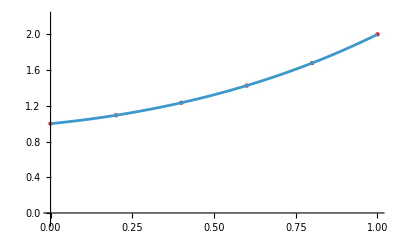

```mathematica
Remove["Global`*"]
ode=y''[x]==Sqrt[1+y'[x]^2];
{a,b,ya,yb}={0.,1.,1,2.};
n=5;
h=(b-a)/n;
dy=(y[i+1]-y[i-1])/(2h);
d2y=(y[i+1]-2*y[i]+y[i-1])/h^2;
ekv=Table[ode/.{x->a+i*h,y''[x]->d2y,y'[x]->dy,y[x]->y[i]},{i,1,n-1}]
sol=NSolve[ekv/.{y[0]->ya,y[n]->yb}][[1]]
yFdm=Table[{i/n,y[i]},{i,0,n}]/.sol/.{y[0]->ya,y[n]->yb}
lp=ListPlot[yFdm,PlotStyle->{Red,PointSize[Medium]},PlotRange->{-0.1,2.2}];
yM=y[x]/.NDSolve[{ode,y[a]==ya,y[b]==yb},y[x],x][[1]];
pl=Plot[yM,{x,a,b},PlotRange->{-0.1,2.2}];
Show[lp,pl]
```

### Exempel 5

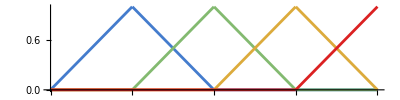

A = (8 | -4 | 0 | 0
-4 | 8 | -4 | 0
0 | -4 | 8 | -4
0 | 0 | -4 | 4),  u = (7/32
3/8
15/32
1/2),  b = (1/4
1/4
1/4
1/8)

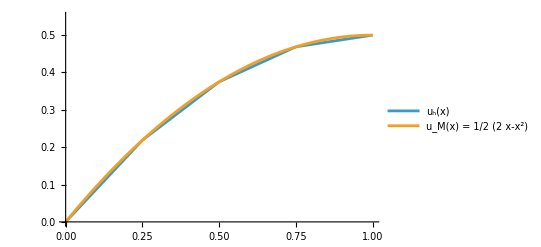

```mathematica
Remove["Global`*"]
n=4;
h=1/n;
f=1;
ode=-y''[x]==f;
(* Hattfunktionerna *)
xv=Table[i*h,{i,0,n}];
phi[i_,x_]=Piecewise[{{(x-(i-1)*h)/h,(i-1)*h<=x<i*h},{((i+1)*h-x)/h,i*h<=x<(i+1)*h}}];
phiplots={};
For[i=1,i<=n,++i,
AppendTo[phiplots,Plot[Evaluate[phi[i,x]],{x,0,1},PlotRange->{0,1},AspectRatio->h,PlotStyle->ColorData["Rainbow"][i/n]]]
]
phip=Show[phiplots]
(* Assemblering *)
a=1/h*SparseArray[{Band[{1,1}]->2,Band[{1,2}]->-1,Band[{2,1}]->-1  },{n,n}];
a[[n,n]]=1/h; 
b={};
For[i=1,i<=n,++i,
AppendTo[b,Integrate[f*Evaluate[phi[i,x]],{x,0,1}]]
]
(* Beräkning av uh *)
u=LinearSolve[a,b];
 uh[x_]=Sum[u[[i]]*phi[i,x],{i,1,n}];
(* Lösning med DSolve *)
uM=y[x]/.DSolve[{ode,y[0]==0,y'[1]==0},y[x],x][[1]];
Print["A = ",MatrixForm[a],",  u = ",MatrixForm[u], ",  b = ",MatrixForm[b]]
Plot[{uh[x],uM},{x,0,1},PlotRange->{0,0.55},PlotLegends->{"u_h(x)",Row[{"u_M(x) = ",TraditionalForm[uM]}]}]
```